# Positive Autoregulation - Demonstrating Bistability

## Copyright Prof. Lee Bardwell -Graphics-

Here we focus on how to demonstrate that this system has more than one steady state, and how to demonstrate the stability (or lack thereof) of these steady states.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* First describe the system *)

pY =Pmax*Y[t]^n/(k^n+Y[t]^n); (* input function for positive autoregulation *)

system1 = {

Y'[t] == pY - r*Y[t]

};

initials1 = {Y[0]==Yzero};

fullsystem = Join[system1,initials1];
```

## Plot the solution Now we solve with NDSolve and plot the resulting numerical solution Compare the results when Yzero→ 0 to when Yzero gets any small positive value

```mathematica
parameters1a = {Pmax->10,k->5,r->1,n->1,Yzero-> 0};
parameters1b = {Pmax->10,k->5,r->1,n->1,Yzero-> 0.05};solution1 = NDSolve[fullsystem/.parameters1a,Y[t],{t,0,20}];
solution2 = NDSolve[fullsystem/.parameters1b,Y[t],{t,0,20}];
```

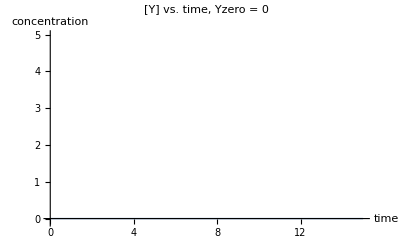

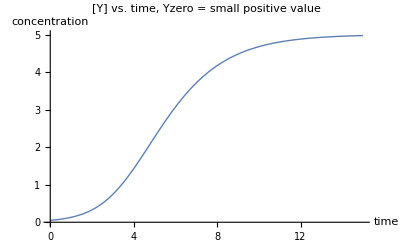

```mathematica
Plot[{Y[t]/.solution1},{t,0,15},PlotStyle->Thick,PlotRange->{-0.1,5},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, Yzero = 0"]
Plot[{Y[t]/.solution2},{t,0,15},PlotStyle->Thick,PlotRange->{0,5},AxesLabel->{"time","concentration"},PlotLabel->"[Y] vs. time, Yzero = small positive value"]
```

## Manipulate-able Time Course Now we Manipulate the NDSolved solution Note how the graph “flips” between steady states as you change the value of Yzero Note how the value of n affects the where the flip occurs

```mathematica
Manipulate[
parameters3 = {Pmax->PmaxValue,k->kValue,r->1,n->nValue, Yzero->YzeroValue};
solution3 = NDSolve[fullsystem/.parameters3,Y[t],{t,0,100}];
Plot[{Y[t]/.solution3,PmaxValue},{t,0,Tmax},PlotStyle->{{Blue,Thick},{Orange,Thick, Dashed}},PlotRange->{0,10},AxesLabel->{"time","[Y]"},PlotLabel->"[Y] vs. time, Y is regulated by itself"],
{{PmaxValue,10},1,10,Appearance->"Labeled"},
"Dashed orange line = simple regulation steady state",
Delimiter,
{{YzeroValue,0.1},0,10,0.1,Appearance->"Labeled"},
"Change this value to see flipping between steady-states",
Delimiter,
{{kValue,4},0.1,10,Appearance->"Labeled"},
{nValue,1,20,1,Appearance->"Labeled"},

{{Tmax,10},10,100,Appearance->"Labeled"}
]
```

## Input-Output Curve Now we make an input-output (dose-response) curve The input here is Yzero and the output is the steady state amount of Y This method uses the Table function to call NDSolve 100 times and store the values in a Table Compare the results when n→2 to when n→1

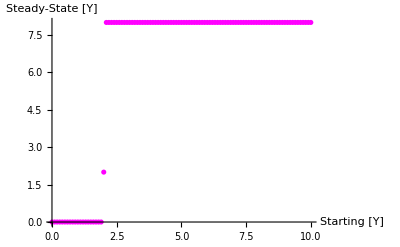

```mathematica
parameters4= {Pmax->10,k->4,r->1,n->2,Yzero-> i};
table1= Table[{i, Y[t] /.Flatten[NDSolve[fullsystem/.parameters4, {Y[t]}, {t, 0, 20}]] /.t -> 20(*get steady-state value*)}, {i, 0, 10, 0.1}];
ListPlot[table1, PlotRange -> All, (*Joined-> True,*)PlotStyle -> {Magenta, Thick},
AxesLabel->{"Starting [Y]","Steady-State [Y]"}]
```

## Manipulate-able Input-Output Curve Here’s how to make a Manipulatable input-output curve for those who are interested

```mathematica
Manipulate[
parameters5 = {Pmax->10,k->kValue,r->1,n->nValue,Yzero-> i};
table2= Table[{i, Y[t] /.Flatten[NDSolve[fullsystem/.parameters5, {Y[t]}, {t, 0, 20}]] /.t -> 20(*get steady-state value*)}, {i, 0, 10, 0.25}];
ListPlot[table2, PlotRange -> {0,12}, (*Joined-> True,*)PlotStyle -> {Magenta, Thick},
AxesLabel->{"Starting [Y]","Steady-State [Y]"}],
{{kValue,3},0.1,10,0.1,Appearance->"Labeled"},
{{nValue,1},1,40,1,Appearance->"Labeled"}
]
```